```mathematica
ClearAll["Global`*"]
```

# Jacobi Elliptic Functions

## According to the definition, m=k^2 Usage-> k^2 for the second argument

```mathematica
plotPath="/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures";
export[object_,name_]:=Export[StringTemplate["``/``.pdf"][plotPath,name],object,ImageResolution->1200];
```

```mathematica
sn[q_,k_]:=JacobiSN[q,k^2];
cn[q_,k_]:=JacobiCN[q,k^2];
dn[q_,k_]:=JacobiDN[q,k^2];
period[k_]:=NIntegrate[1/Sqrt[1-k^2Sin[x]^2],{x,0,π/2}];
```

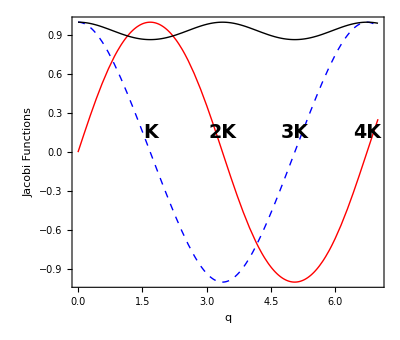

```mathematica
f1[k_]:=Plot[{sn[q,k],cn[q,k],dn[q,k]},{q,0,7},Frame->True,Axes->{True,False},AspectRatio->0.85,FrameStyle->Directive[Black,Thick],FrameLabel->{"q","Jacobi Functions"},LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},PlotStyle->{{Red,Thick},{Blue,Thick,Dashed},{Black,Thick}},Epilog->{Inset[Style["K",19,Bold,Black,Italic],{period[k],0.15}],Inset[Style["2K",19,Bold,Black,Italic],{2*period[k],0.15}],Inset[Style["3K",19,Bold,Black,Italic],{3*period[k],0.15}],Inset[Style["4K",19,Bold,Black,Italic],{4*period[k],0.15}]}];
Show[f1[1/2]]
export[f1[1/2],"Jacobi-Elliptic-Functions"];
```

```mathematica
period[1/2]
```

1.68575